```mathematica
(*PrependTo[$Path,"/Users/annils14/Documents/KerrModes"];*)PrependTo[$Path,"/home/cookgb/Research/KerrQNM/KerrModes"];
Needs["KerrTTMR`"]
SetSpinWeight[2]
```

All KerrMode routines (TTMR) set for Spin-Weight s = 2

```mathematica
SchTTMRTable[2]=2;
SchTTMRTable[2,0]={0.372-0.094*I,0,0,0,0};
SchTTMRTable[2,1]={0.347-0.272*I,0,0,0,0};
SchTTMRTable[3]=2;
SchTTMRTable[3,0]={0.6-0.09*I,0,0,0,0};
SchTTMRTable[3,1]={0.6-0.28*I,0,0,0,0};
```

```mathematica
$MinPrecision=24
```

24

```mathematica
Plot3D[Abs[PlotContFrac[0,2,0,0,0,ωr -ⅈ ωi,300,15]],{ωr,-0.001,0.001},{ωi,1.999,2.001}]
```

-Graphics3D-

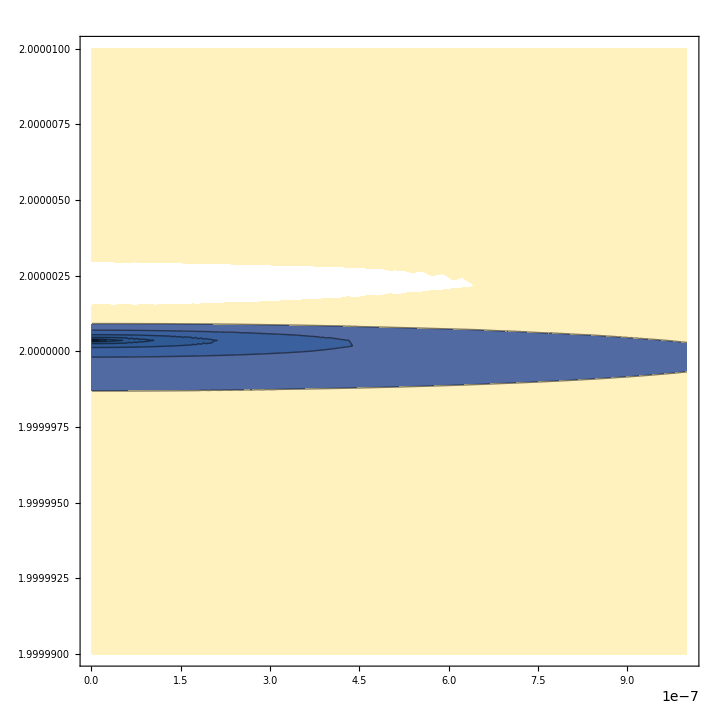

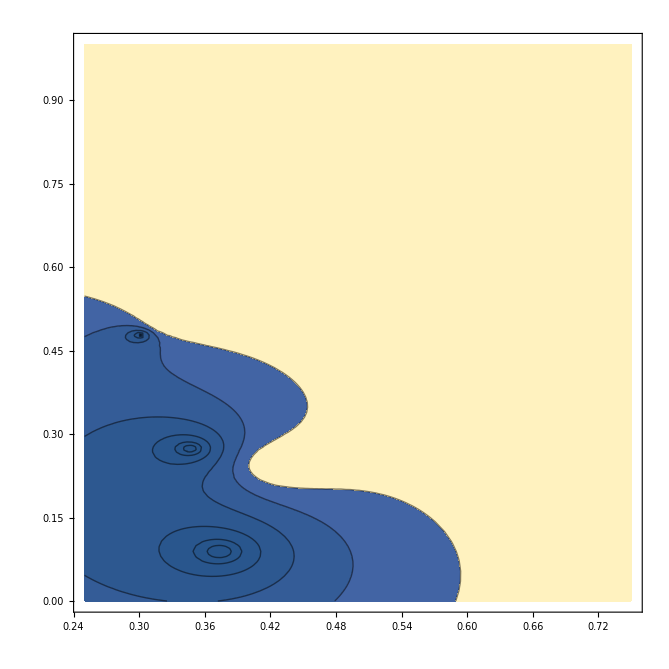

```mathematica
ContourPlot[Abs[PlotContFrac2[0,2,0,1/2^11,1,ωr-ⅈ ωi,300,15]],{ωr,10^(-9),10^-6},{ωi,2-10^(-5),2+10^(-5)},Contours->{1/8,1/4,1/2,1,2,4,8}]
```

```mathematica
Plot3D[{Re[PlotContFrac2[0,2,0,0,1,ωr-ⅈ ωi,300,15]],Im[PlotContFrac2[0,2,0,0,1,ωr-ⅈ ωi,300,15]]},{ωr,0.037,0.0374},{ωi,0.092,0.096}]
```

-Graphics3D-

```mathematica
Plot3D[{Re[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]],Im[RadialCFRem[0,-2,0,0,4,ωr-ⅈ ωi,300][[1]]]},{ωr,0,4},{ωi,0,4}]
```

-Graphics3D-

```mathematica
RadialCFRem[0,-2,0,0,10,-ⅈ 10,2]
```

{0,2}

```mathematica
RadialCFRem[0,2,0,0,4,0.0372-ⅈ 0.094,300]
```

RadialCFRem[0,2,0,0,4,0.0372-0.094 ⅈ,300]

```mathematica
SchwarzschildTTMR[2,0,RadialDebug->1,SchDebug->0]
```

Computing (l=2,n=0)

δω= 0.00156291110201406828110118+0.00510613133482066957985743 ⅈ root= 0.12030556005741694101633

δω= 0.00130855158078940489317997+0.00412714276147985338306565 ⅈ root= 0.0977524363525932384858621

δω= 0.00103594454167295373056286+0.00315551654631708473720952 ⅈ root= 0.0751502749571679139297367

δω= 0.000745337167685731180102232+0.00219159174910191306407745 ⅈ root= 0.0524976796308841772827079

δω= 0.000436730897733925209220932+0.00123578115660854151841983 ⅈ root= 0.0297932642238750083975482

δω= 0.000109336118593342555606563+0.000288786234059965613085436 ⅈ root= 0.00703591413375007183401605

δω= 3.29490029123822078502697×10^-7-2.55383024386891230341558×10^-7 ⅈ root= 9.50610609708662277090294×10^-6

δω= -2.37458595949650936754899×10^-13+7.20240046897876565259863×10^-13 ⅈ root= 1.72934939254777430405789×10^-11

δω= -4.45247939405721967128392×10^-23+1.16248025941627939815106×10^-22 ⅈ root= 2.83863477339011706241109×10^-21

{0.373671684418041835793492-0.0889623156889356982804609 ⅈ,0,300,-14,1.24483174809995174176253×10^-22}

```mathematica
SchwarzschildTTMR[2,1,RadialDebug->0,SchDebug->0]
```

Computing (l=2,n=1)

{0.346710996879163439717677-0.273914875291234817349562 ⅈ,1,300,-14,3.03397134986387404478357×10^-21}

```mathematica
SchwarzschildTTMR[2,7]
```

Computing (l=2,n=2)

{0.301053454612366393764361-0.478276983223071809827295 ⅈ,2,300,-14,3.50976556069587809302063×10^-22}

Computing (l=2,n=3)

{0.251504962185590392029622-0.705148202433496003430767 ⅈ,3,300,-14,1.25435674943564289526196×10^-21}

Computing (l=2,n=4)

{0.207514579813070544996171-0.946844890866355732712142 ⅈ,4,417,-14,1.853460004231019771871×10^-23}

Computing (l=2,n=5)

{0.169299403093043721217619-1.19560805413584821014624 ⅈ,5,772,-14,1.1984630984649905188328×10^-21}

Computing (l=2,n=6)

{0.133252340245187704204216-1.4479106261620379511222 ⅈ,6,1425,-14,1.48902912475939482549437×10^-19}

Computing (l=2,n=7)

{0.0928223336702009444280507-1.70384117220613552851653 ⅈ,7,4428,-14,1.26993519011069264142531×10^-17}

```mathematica
?SchwarzschildTTML
```

SchwarzschildTTML[l,n] computes the Quasi-Normal Mode solutions for overtone n of mode l.  The mode is computed to an accuracy of 10^-14.  For given 'l', if solutions with overtones (n-1) and (n-2) have not been computed, then the routine is recersively called for overtone '(n-1).  If no solutions exist for mode l, then the first two overtones of (l-1) and (l-2) are used to extrapolate initial guesses for these modes.

Options:
	 SpinWeight→Null : -2,-1,0
		 The spin weight must be set via a call to SetSpinWeight before any KerrTTML
		 function call.
	 ModePrecision→24
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 RadialCFMinDepth→300
		 The minimum value for the Radial Continued Fraction Depth.
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial value by that
		 fraction.  Integer values larger than RadialCFMinDepth are used as the new
		  initial value.
	 RadialRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
	 Rootϵ→-14
		 10^Rootϵ is the maximum allowed magnitude for the Radial Continued Fraction.
	 SchDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Schwarzschile iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.

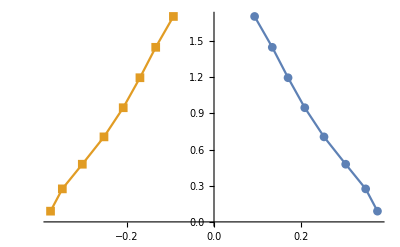

```mathematica
PlotSchTTMR[2]
```

```mathematica
Options[PlotSchTTMR]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,Epilog→{},Filling→None,FillingStyle→Automatic,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotSpinWeight→-2,PlotStyle→Automatic,KerrModes`Private`PlotTable→Null[],PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},DisplayFunction:>$DisplayFunction,FormatType:>TraditionalForm,PerformanceGoal:>$PerformanceGoal,PlotTheme:>$PlotTheme}

```mathematica
?SchTTMRTable
```

Global`SchTTMRTable

SchTTMRTable[2]=8
 
SchTTMRTable[3]=2
 
SchTTMRTable[2,0]={0.373671684418041835793492-0.0889623156889356982804609 ⅈ,0,300,-14,1.24483174809995174176253×10^-22}
 
SchTTMRTable[2,1]={0.346710996879163439717677-0.273914875291234817349562 ⅈ,1,300,-14,3.03397134986387404478357×10^-21}
 
SchTTMRTable[2,2]={0.301053454612366393764361-0.478276983223071809827295 ⅈ,2,300,-14,3.50976556069587809302063×10^-22}
 
SchTTMRTable[2,3]={0.251504962185590392029622-0.705148202433496003430767 ⅈ,3,300,-14,1.25435674943564289526196×10^-21}
 
SchTTMRTable[2,4]={0.207514579813070544996171-0.946844890866355732712142 ⅈ,4,417,-14,1.853460004231019771871×10^-23}
 
SchTTMRTable[2,5]={0.169299403093043721217619-1.19560805413584821014624 ⅈ,5,772,-14,1.1984630984649905188328×10^-21}
 
SchTTMRTable[2,6]={0.133252340245187704204216-1.4479106261620379511222 ⅈ,6,1425,-14,1.48902912475939482549437×10^-19}
 
SchTTMRTable[2,7]={0.0928223336702009444280507-1.70384117220613552851653 ⅈ,7,4428,-14,1.26993519011069264142531×10^-17}
 
SchTTMRTable[3,0]={0.6-0.09 ⅈ,0,0,0,0}
 
SchTTMRTable[3,1]={0.6-0.28 ⅈ,0,0,0,0}